# Fisher Matrix for multiple tracers

Raul Abramo and Luca Amendola  arXiv : xxxx.yyyy

This notebook produces the model-independent Fisher matrix (per unit phase-space volume) for the band power-spectrum P and the redshift distortion parameter beta, for a single tracer, and, similarly, for the total spectrum P and beta_(1,2)  for two tracers. The parameters are actually the log of these quantities, so the output gives directly the relative errors. In particular, the notebook plots the relative, marginalized error on the redshift distortion parameter beta, both for the single- and the two-tracer case. This should correspond to Fig. 2, right panel, of the paper. The entire notebook runs in about 5 minutes on a laptop.
Use of this notebook is free. If you use it in a publication, please cite the aper above.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luca/Dropbox/active-project-fisher-multipletracers/paper1/mathematica

## Single tracer

```mathematica
(* all spectra in units of noise*bias^2; log P, log beta as parameters *)
```

```mathematica
ClearAll["Global`*"];

faca=1+betaa*mu^2;

ppar={pa,betaa};

npar=Length[ppar];

na=1+1/faca^2/pa; 

(* correlation matrix *)

 c=Simplify[{{0,faca^2*pa*na},{faca^2*pa*na,0}}];

c//TableForm

n=Length[c];gamma=Simplify[Table[Inverse[c][[i,m]]*Inverse[c][[j,l]],{i,n},{j,n},{l,n},{m,n}]];

(* analytical fisher matrix *)

fisher1[pa_,betaa_]=Simplify[PowerExpand[Simplify[(1/2)*Table[Integrate[Simplify[Sum[ppar[[a]]*ppar[[b]]*D[c[[i,j]],ppar[[a]]]*D[c[[l,m]],ppar[[b]]]*gamma[[i,j,l,m]],{i,n},{j,n},{l,n},{m,n}]],{mu,-1,1},GenerateConditions->False]/2,{a,npar},{b,npar}]]]];

 (*  marginalized relative error on beta_1 and p *)

Clear[errbeta1];errbeta1[pa_,betaa_]=Simplify[Inverse[fisher1[pa,betaa]][[2,2]]];
errp1[pa_,betaa_]=Simplify[Inverse[fisher1[pa,betaa]][[1,1]]];
```

0 | 1+(1+betaa mu^2)^2 pa
1+(1+betaa mu^2)^2 pa | 0

## Two tracers

```mathematica
(* fisher matrix estimate *)
Clear[p11,p12,p22,p34,p23];faca=1+betaa*mu^2;facb=1+betab*mu^2;

(* all spectra in units of noise*bias^2 *)


(* parameters are log P, log beta1, log beta2 *)

ppar={pt,betaa,betab};

npar=Length[ppar];

(* q=n2/n1 *)
pa=pt/((1+betaa/betab*q)^2/(1+q));
pb=pt*betaa^2/betab^2*q/((1+betaa/betab*q)^2/(1+q));

na=1+1/faca^2/pa;nb=1+1/facb^2/pb;

(* correlation matrix *)

c=Simplify[PowerExpand[{{0,faca^2*pa*na,0,faca*facb*Sqrt[pa*pb]},{faca^2*pa*na,0,faca*facb*Sqrt[pa*pb],0},{0,faca*facb*Sqrt[pa*pb],0,facb^2*pb*nb},{faca*facb*Sqrt[pa*pb],0,facb^2*pb*nb,0}}]];

n=Length[c];gamma=Simplify[Table[Inverse[c][[i,m]]*Inverse[c][[j,l]],{i,n},{j,n},{l,n},{m,n}]];

(* numerical  Fisher matrix *)

Clear[fmu,betaa,betab];fmu[betaa_,betab_,pt_,q_]=Table[Simplify[Sum[ppar[[a]]*ppar[[b]]*D[c[[i,j]],ppar[[a]]]*D[c[[l,m]],ppar[[b]]]*gamma[[i,j,l,m]],{i,n},{j,n},{l,n},{m,n}]],{a,npar},{b,npar}];

fisher2[betaa_,betab_,pt_,q_]:=(1/2)*Table[NIntegrate[fmu[betaa,betab,pt,q][[a,b]],{mu,-1,1}]/2,{a,npar},{b,npar}];
invfisher2[betaa_,betab_,pt_,q_]:=Inverse[(1/2)*Table[NIntegrate[fmu[betaa,betab,pt,q][[a,b]],{mu,-1,1}]/2,{a,npar},{b,npar}]];

(* marginalized relative variance of pt, beta_1, beta_2, and correlation *)

errp2[betaa_,betab_,pt_,q_]:=invfisher2[betaa,betab,pt,q][[1,1]];
errbeta12[betaa_,betab_,pt_,q_]:=invfisher2[betaa,betab,pt,q][[2,2]];
errbeta22[betaa_,betab_,pt_,q_]:=invfisher2[betaa,betab,pt,q][[3,3]];
errbetacorr2[betaa_,betab_,pt_,q_]:=invfisher2[betaa,betab,pt,q][[2,3]];


(* variance average beta *)

eab2[betaa_,betab_,pt_,q_]:=(betab^2*errbeta12[betaa,betab,pt,q]+q^2*betaa^2*errbeta22[betaa,betab,pt,q]+2*q*betaa*betab*errbetacorr2[betaa,betab,pt,q])/(betab+betaa*q)^2;
```

## Check and plot

```mathematica
(* quick check: this should give 25.329 *)

errbeta12[1,1,1,1]
```

25.329

```mathematica
(* this plot should produce Fig. 1 of the paper *)
```

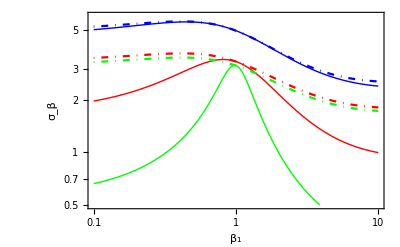

```mathematica
Clear[betaa,betab,pt,q];
(* this is an arbitrary choice for q, see paper *)
q[ba_,bb_]:=bb^2/ba^2;
(* this is the average weighted single beta *)
bas[ba_,bb_]:=(1+q[ba,bb])*ba*bb/(bb+q[ba,bb]*ba);

LogLogPlot[{Sqrt[Chop[eab2[ba,1.,1.,q[ba,1]]]],Sqrt[Chop[eab2[ba,1.,10.,q[ba,1]]]],Sqrt[Chop[eab2[ba,1.,100.,q[ba,1]]]],Sqrt[Chop[errbeta1[1,bas[ba,1]]]],Sqrt[Chop[errbeta1[10,bas[ba,1]]]],Sqrt[Chop[errbeta1[100,bas[ba,1]]]]},{ba,.1,10},PlotStyle->{{Blue,Thick},{Red,Thick},{Green,Thick},{Blue,DotDashed},{Red,DotDashed},{Green,DotDashed}},PlotRange->{.5,6},Frame->True,FrameLabel->{Subscript[β, 1],Subscript[σ, β]},BaseStyle->{16,FontFamily->"Times"}]
```

## Output for general parameters

After running the previous code, you can obtain here the numerical results for any 
choice of parameters.

```mathematica
(* Choose the parameter values *)
betaa=1.;betab=0.1; pt=10.;
q=1.;
```

```mathematica
(* Fisher 1 tracer *)
Chop[fisher1[pt,betaa]]
```

```mathematica
(* Fisher 2 tracers *)
fisher2[betaa,betab,pt,q]
```

```mathematica
(* variance of beta, 1 tracer *)
Chop[errbeta1[pt,betaa]]
(* variance of pt, 1 tracer *)
Chop[errp1[pt,betaa]]
```

```mathematica
(* variance of beta1, 2 tracers *)
errbeta12[betaa,betab,pt,q]
(* error on beta2, 2 tracers *)
errbeta22[betaa,betab,pt,q]
(* error on combined beta, 2 tracers *)
eab2[betaa,betab,pt,q]
(* error on pt, 2 tracers *)
errp2[betaa,betab,pt,q]
```